################################################[----FEM n=10 h=1/10 t=t_begin----]################################################

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x = 1..

M=(0.0666667 | 0.0166667 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0166667 | 0.0666667 | 0.0166667
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0166667 | 0.0333333)

A=(20. | -10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-10. | 20. | -10. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -10. | 20. | -10. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -10. | 20. | -10. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -10. | 20. | -10. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -10. | 20. | -10. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -10. | 20. | -10. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -10. | 20. | -10. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -10. | 20. | -10.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -10. | 10.)

M+Θ*(△t)/2*A=(0.566667 | -0.233333 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.233333 | 0.566667 | -0.233333 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.233333 | 0.566667 | -0.233333 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.233333 | 0.566667 | -0.233333 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.233333 | 0.566667 | -0.233333 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.233333 | 0.566667 | -0.233333 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.233333 | 0.566667 | -0.233333 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.233333 | 0.566667 | -0.233333 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.233333 | 0.566667 | -0.233333
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.233333 | 0.283333)

Pohidna=π Cos[π x]

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in x in the region {{0.,1.}}. NIntegrate obtained 0. and 0. for the integral and error estimates.

Part::pkspec1: The expression j cannot be used as a part specification.

Part::pkspec1: The expression 1+j cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in x in the region {{0.,1.}}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

F={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

q1={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

q2={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

u_n(x)=0.

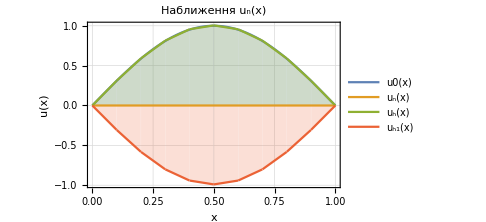

```mathematica
a=0;b=1;
ρ=1; Subscript[T, 0]=1; Θ=1/2;
 u0[x_]:=Sin[Pi*x]; v0[x_]:=0; p[x_,t_]:=0;
ti=1; deltat=1/10;
n = 10;
$MaxPiecewiseCases=700;
(*Функції Куранта*)
ϕ[x0_,i0_] :=
Module[{x=x0, i=i0, k, m},k=i+1; m=i-1;
Piecewise[{
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧}, {0,x<w⟦i⟧ || x>w⟦k⟧}}],i≠ 1 && i≠n+1}, 
{Piecewise[{{(w⟦k⟧-x)/(w⟦k⟧-w⟦i⟧),w⟦i⟧≤x≤w⟦k⟧},{0,w⟦k⟧<x≤1}}], i==1},
{Piecewise[{{(x-w⟦m⟧)/(w⟦i⟧-w⟦m⟧), w⟦m⟧≤x≤w⟦i⟧},{0,0≤x<w⟦i⟧}}], i==n+1}
}]];
h = (b-a)/n;
w = Table[a+i*h, {i,0,n}];
Print["################################################[----FEM n=",n," h=",h, " t=",Subscript[t, begin],"----]################################################"];
matrixM = SparseArray[{{i_,j_}/;Abs[i-j]≤1->NIntegrate[ρ*ϕ[x,i+1]*ϕ[x,j+1],{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
matrixA= SparseArray[{{i_,j_}/;Abs[i-j]≤1->NIntegrate[Subscript[T, 0]*D[ϕ[x,i+1], x]*D[ϕ[x,j+1], x],{x,a,b}, Method->"DoubleExponential"]}, {n,n},0.];
Print["M=",MatrixForm[matrixM]];
Print["A=",MatrixForm[matrixA]];
matrixTotal = matrixM+Θ*deltat/2*matrixA;
Print["M+Θ*(△t)/2*A=",MatrixForm[matrixTotal]];
ui[x_]:=1; vi[x_]:=1;
Print["Pohidna=",D[u0[x], x]];
F = Table[NIntegrate[p[x,ti]*ϕ[x,i+1],{x,a,b}, Method->"DoubleExponential"]-
NIntegrate[Subscript[T, 0]*D[ui[x], x]*D[ϕ[x,j+1], x],{x,a,b}, Method->"DoubleExponential"]-
deltat*Θ*NIntegrate[Subscript[T, 0]*D[vi[x], x]*D[ϕ[x,j+1], x],{x,a,b}, Method->"DoubleExponential"], {i,1,n}];
Print["F=",F];
q1 = LinearSolve[matrixA,F];
q2 = LinearSolve[matrixTotal,F];
Print["q1=",q1];
Print["q2=",q2];
Subscript[u, n][x_]:=∑_(i=1)^n q2[[i]]*ϕ[x,i+1];
Print["u_n(x)=",Subscript[u, n][x]];
Subscript[u, h][x_]:=∑_(i=1)^n (u0[w⟦i+1⟧]+deltat*(deltat/2*u0[w⟦i+1⟧]+v0[w⟦i+1⟧]))*ϕ[x,i+1];
Subscript[v, h][x_]:=2*((Subscript[u, n][x]-u0[x])/deltat)-v0[x];
Subscript[u, h1][x_]:=∑_(i=1)^n (Subscript[u, h][w⟦i+1⟧]+deltat*(deltat/2*u0[w⟦i+1⟧]+Subscript[v, h][w⟦i+1⟧]))*ϕ[x,i+1];
difference1 = Plot[{u0[x],Subscript[u, n][x],Subscript[u, h][x],Subscript[u, h1][x]}, {x,a,b}, FrameLabel->{"x ","u(x) "},PlotLegends->"Expressions",PlotLabel->Style[Framed["Наближення u_n(x)"]],Background->White,Filling->Axis,Frame->True,GridLines->Automatic,PlotRange->All, ImageSize->Medium];
Print[difference1];
```